Hi all,
This notebook is used to parse your CFG data, all the way from raw data on the server to a neat 31-column csv file on you local machine.
Throughout the notebook you will find elaborate explanations and comments, designed to help you achieve two goals:
	1. Parse, extract measures and export your data while updating requisite shared files, with as little hassle as possible.
	2. Understand some of how the parser works, and hopefully learn a little Mathematica syntax while doing so.
Please follow the instructions closely, and feel free to contact Roy for further assistance and explanations.

## Individual Definitions

This blocks will initiate the required variables with the info supplied in your localInfo.mx file. If you have no idea what that is, please refer to generateLocalInfoFile.nb.

```mathematica
parserDir = NotebookDirectory[];
repoDir = ParentDirectory@parserDir;
dataDir = FileNameJoin[{repoDir, "ParsedData"}];
homeDir = SetDirectory[ParentDirectory@repoDir];
datasetName = datasetName="TTT"
<<ParserUtils`
```

TTT

## Pre-process

```mathematica
rawData=Import["N:\\Experiments\\CFG_TTT\\raw\\event.csv"];
Print["Total entries: ", rawData//Length]
```

Total entries: 109450

Omit rows that only indicate startfeedback or done selection and represent no game data. Gather results by playerCustomData to create a 3D structure where each entry is a list of a given player’s games (for various reasons, some have more than one), sorted by userTime. Each “game” is a list of the 24 variables the game collects.

```mathematica
data=SortBy[#,#[[3]]&]&/@GatherBy[DeleteCases[rawData[[2;;]],{___,"startfeedback"|"done selection",___}],#[[11]]&];
Print["Total participants: ",( currentIDs=DeleteDuplicates@data[[;;,1,10]])//Length]
```

Total participants: 424

Remove games with no data, AKA no startsearch entry:

```mathematica
data=Select[data,Length@#>2&]; (* Remove empty games *)
data=Select[data,MemberQ[#[[;;,12]],"startsearch"]&]; (* Remove games with only tutorial data, no real game data *)
Print["IDs removed: ", currentIDs~Complement~(currentIDs=DeleteDuplicates@data[[;;,1,10]])]
```

IDs removed: {99999,236953,237461,1139595,1235545,2202005,2308269,3036754,4169678,4232578,4345498,5042882,5176308,5414339,5755639,5841477,6664273}

Remove unfinished games:

```mathematica
Print["Ran through the entire game: ",Length@(data=Select[data,Union@Split[DeleteCases[#[[;;,12]],"end search"|"selected shape"],#2=!="startsearch"&][[2]]=={"added shape to gallery","movedblock","startsearch"}&])];
Print["IDs removed: ", currentIDs~Complement~(currentIDs=DeleteDuplicates@data[[;;,1,10]])]
```

Ran through the entire game: 372

IDs removed: {91550,784404,1263392,1378286,1783040,2401806,2471412,3170134,3469610,3657878,3844203,3860254,4033784,4214889,4600226,4840417,4960570,5145980,5145981,5336763,5573802,5608469,5842242,6156854,6277159,6354932,7307440,7502508,7561318,7603355,7603811,8233107,9030616,9080144,9103901,9610012,9838776,TEST}

Remove games with shapes where not all 10 squares are connected. Shapes with disconnected squares should not be possible, if this part finds and removes such games that means we have a bug in the game, report ASAP!

```mathematica
Print["All shapes are tenminos: ",Length@(data=Select[data,DeleteDuplicates@(Cases[#,{___,"movedblock",___}][[;;,19]]/.x_String:>Length@ToExpression@StringReplace[x,{"["->"{","]"->"}"}])=={10}&])];
Print["IDs removed: ", currentIDs~Complement~(currentIDs=DeleteDuplicates@data[[;;,1,10]])]
```

All shapes are tenminos: 372

IDs removed: {}

## Parse

Parse and store the result sorted by IDs:

```mathematica
Print["After parsing: ",
Length@(parsedData=SortBy[Parse[#,URLid->True]&/@data,#1&])];
Print["IDs not in parsed dataset: ", currentIDs~Complement~(currentIDs=parsedData[[;;,1]])]
```

After parsing: 372

IDs not in parsed dataset: {}

## Filter

Remove data stored in server before the current study. Should remove nothing is everything was properly set in localInfo.mx:

```mathematica
filteredData=Select[parsedData,DateObject["2020-04-18T00:00:00.000Z"]<#[[2]]<DateObject["2020-05-10T00:00:00.000Z"]||DateObject["2021-03-13T00:00:00.000Z"]<#[[2]]<DateObject["2021-05-25T00:00:00.000Z"]&];
Print["IDs removed: ", currentIDs~Complement~(currentIDs=filteredData[[;;,1]])]
```

IDs removed: {12190,12414,17654,22264,105039,108744,121505,123403,207978,212121,212244,219462,265096,347571,366243,393126,492882,499911,509710,589132,603821,645954,662342,705567,706080,791874,796960,831750,851174,901012,922701,999999,1026298,1035204,1038317,1200575,1230308,1369686,1398899,1446403,1456422,1490369,1599621,1603421,1607162,1712480,1760836,1889255,1942363,1976632,2012762,2107941,2112453,2118331,2132932,2156755,2206143,2228277,2241988,2283633,2384785,2397116,2450974,2467736,2495890,2511119,2568399,2597936,2599499,2640719,2661716,2693648,2710740,2741837,2795853,2883610,2884368,2933414,2933511,3014111,3054440,3097412,3171778,3202342,3274288,3384791,3462537,3467353,3579788,3585523,3629544,3689187,3689548,3764087,3772109,3832571,3861103,3980188,4017152,4035690,4095733,4153923,4251369,4276325,4287208,4311962,4401407,4555246,4686732,4748958,4815502,4942394,4970414,4972139,5024757,5038031,5110314,5120895,5135488,5165171,5222301,5446637,5494993,5537643,5623814,5646739,5686750,5715111,5724912,5744945,5765080,5844146,5844330,5846484,5898680,5971512,6076382,6126119,6138673,6146961,6161926,6178668,6198451,6214796,6232599,6235694,6241503,6319539,6351470,6384946,6389942,6444924,6449435,6472726,6473353,6552819,6581276,6655203,6761188,6768578,6790295,6868441,6873431,6879653,6938657,7072004,7098942,7120540,7165853,7177423,7201766,7210951,7254645,7259347,7356948,7374432,7458147,7561345,7623707,7639154,7894069,7910430,7977391,7982172,8006934,8021074,8137079,8214109,8220944,8304452,8338336,8381116,8412949,8431571,8523348,8587540,8622715,8657612,8660194,8666269,8734664,8931208,8931316,8938451,8949060,8962705,9002918,9004335,9058031,9069272,9103185,9125304,9136349,9144011,9150212,9153009,9159584,9212679,9233976,9240087,9253535,9267485,9270943,9293737,9296083,9336515,9402049,9463279,9492715,9569609,9578984,9589289,9602104,9616160,9627062,9708026,9723203,9731460,9741042,9751557,9778526,9798506,9808045,9813606,9821458,9895929,9938204,9948932,9999999,,${e://Field/Random ID}}

Remove games that produced less than 80 shapes. This is a standard demand we set for a game to be considered sufficient data for analysis.

```mathematica
Print["Moved at least 80 steps: ",
Length@(filteredData = Select[filteredData,Length@#[[3]]≥80&])]
Print["IDs removed: ", currentIDs~Complement~(currentIDs=filteredData[[;;,1]])]
```

Moved at least 80 steps: 115

IDs removed: {3410383,6766547,9649091}

Remove games that lasted less 10 minutes. This is a standard demand we set for a game to be considered sufficient data for analysis.

```mathematica
Print["Played at least 10 min: ",Length@(filteredData = Select[filteredData,#[[3,-1,-1]]≥600&])]
Print["IDs removed: ", currentIDs~Complement~(currentIDs=filteredData[[;;,1]])]
```

Played at least 10 min: 111

IDs removed: {868556,5282523,7302440,8188513}

Remove games that had a break of 1.5min or more:

```mathematica
Print["All breaks shorter than 1.5min: ",
Length@(filteredData=filteredData[[Flatten@Position[Max/@Differences/@(filteredData[[;;,3,4;;-4,2]]),x_/;x<90],;;]])];
Print["IDs removed: ", currentIDs~Complement~(currentIDs=filteredData[[;;,1]])]
```

All breaks shorter than 1.5min: 105

IDs removed: {422893,1888609,6179971,6640303,7342040,8583348}

## Save data & update files

Export parsed data:

```mathematica
Export["N:\\Experiments\\CFG_TTT\\parsed\\parsed_and_filtered.txt",filteredData];
```

We only store shortest paths between shapes that participants actually ever produced. Calculate shortest paths between shapes saved to gallery for the first time in this dataset:

```mathematica
ExtraGallerySP=Cases[(Union@@(Partition[Prepend[ToExpression/@Select[#/.R,Length@#==3&][[;;,1]],1],2,1]&/@parsedData[[;;,3]]))/.AllGallerySP,_List];
```

```mathematica
(AddedGallerySP={##}->GraphDistance[g,##]&@@@ExtraGallerySP);//Timing
```

{0.,Null}

Update shared shortest paths file:

```mathematica
Export[FileNameJoin[{parserDir,"AllGallerySP.txt"}],Join[Normal[AllGallerySP],AddedGallerySP]];
CopyFile[FileNameJoin[{parserDir,"AllGallerySP.txt"}],FileNameJoin[{$UserBaseDirectory,"Applications","AllGallerySP.txt"}],OverwriteTarget->True];
<<ParserUtils`
```

## Exclude outliers

Outliers are filtered only based on the measures of median exploit duration and median explore duration.
We start by calculating those:

```mathematica
clustered = findclusters2/@filteredData;
```

```mathematica
pathsLengths=#[[;;,;;,4]]&/@clustered;
{explore, exploit}=( Median/@({Total/@Split[#,Length@#1==1&][[;;,;;,1]],Total/@Select[#,Length@#>2&][[;;,2;;]]}&@#)&/@pathsLengths)ᵀ;
```

Set number of STDs from mean to filter by:

```mathematica
nStdForOutlier=3;
```

```mathematica
exploreOutliersIdx=Flatten@Position[N@Standardize@explore,_?(#>nStdForOutlier&)];
exploitOutliersIdx=Flatten@Position[N@Standardize@exploit,_?(#>nStdForOutlier&)];
outlierIdx=exploreOutliersIdx∪exploitOutliersIdx;
inlierIdx=Range[Length@filteredData]~Complement~outlierIdx;
```

Filtering:

```mathematica
inlierData=filteredData[[inlierIdx]];
Print["IDs removed: ", filteredData[[;;,1]]~Complement~(currentIDs=inlierData[[;;,1]])]
```

IDs removed: {6764823,8326152,9600597}

View all remaining IDs, sorted to help you easily identify if specific IDs made it or not:

```mathematica
currentIDs
```

{10488,122319,340445,477282,572571,668649,726889,860410,1060404,1108365,1348442,1396376,1458241,1530885,1628596,1692232,1716463,1726165,1864818,1920848,1987252,2133836,2140194,2164676,2168723,2171619,2185902,2257189,2565055,2718385,3064327,3223148,3284103,3317839,3363591,3374464,3567839,3679849,3694176,3755630,3773362,3791727,3887378,4027401,4498909,4531180,4582049,4748029,4816994,4831602,4857595,5221452,5390634,5473307,5751980,5822588,5912234,6011035,6102006,6128847,6169425,6471533,6549967,6717443,6855705,6892224,6919100,7163705,7225713,7289058,7374151,7510218,7541050,7594903,8021243,8098699,8127933,8184961,8286321,8320248,8348861,8461746,8481610,8587581,8614913,8748913,8763383,8782774,8867606,8985203,9203764,9225617,9265689,9355450,9391660,9440877,9442182,9532934,9608752,9608766,9766445,ROY}

```mathematica
inlierData//Length
```

102

## Extract game measures

Hit it, Maestro!

```mathematica
withLabels=extractMeasures@inlierData;
noLabels=Rest@withLabels;
```

Sanity check. Dimensions should be {# subjects, # measures}. If the result is only {# subjects}, there’s a problem.

```mathematica
noLabels//Dimensions
```

{102,39}

Finally, get the promised csv:

```mathematica
withLabels[[1]]=StringReplace[labels,"Δ"->"d"];
Export["N:\\Experiments\\CFG_TTT\\standard_measures\\standard_measures.csv",withLabels];
```

## Explore-exploit duration PCA

Make sure your data behaves as expected (strong correlation between durations of phases):

```mathematica
medianStepsMatrix=noLabels[[;;,{17,18}]];
vanillamedianStepsMatrix=(Import@"C:\\Users\\roygutg\\Documents\\GitRepos\\CFGAnalysisTools\\ParsedData\\vanillaMeasures.csv")[[2;;,17;;18]];
```

```mathematica
<<Scatter`
```

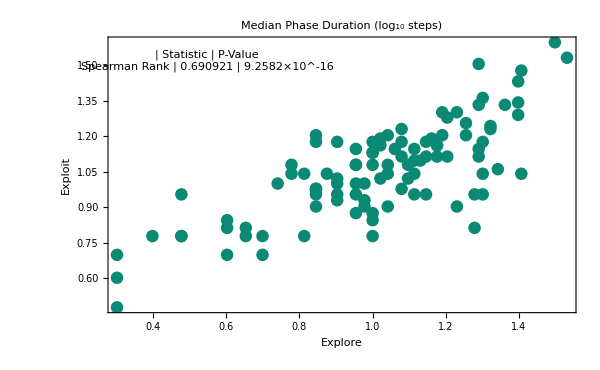

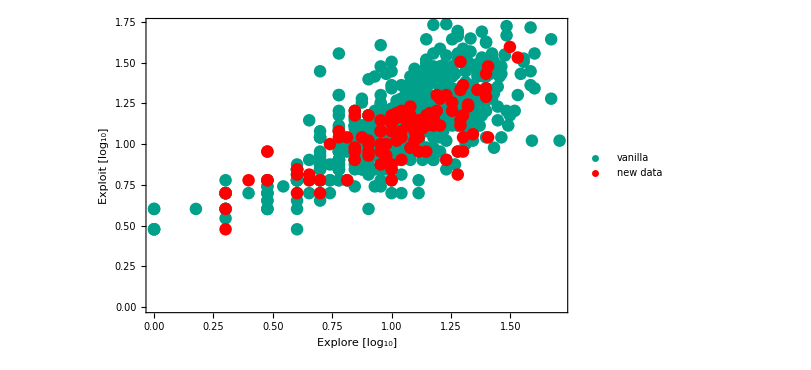

```mathematica
Show[Scatter[Log10@medianStepsMatrix, {"Explore", "Exploit"},ShowRegression->False], PlotLabel->Style[Text["Median Phase Duration (log_10 steps)"],20]]
ListPlot[Log10/@{vanillamedianStepsMatrix,medianStepsMatrix}, Frame -> True, ImageSize -> 600, FrameStyle -> 20, PlotRange -> All, PlotStyle->{{PointSize[0.015],RGBColor["#00A08A"]}, {PointSize[0.015], RGBColor["#FF0000"]}},FrameLabel->{"Explore [log_10]","Exploit [log_10]"},PlotLegends->{"vanilla","new data"}]
```

```mathematica
{pc1,pc2}=PrincipalComponents[medianStepsMatrix,Method-> "Correlation"]ᵀ;
```

```mathematica
#/Total[#]&@((Eigenvalues@Correlation[medianStepsMatrix])^2)(* explained variance per PC *)
```

{0.981183,0.0188172}

PCA does not guarantee the direction of PCs. To suit the name “switching rate”, we want it to decrease as phase durations increase. Let’s look at the trend:

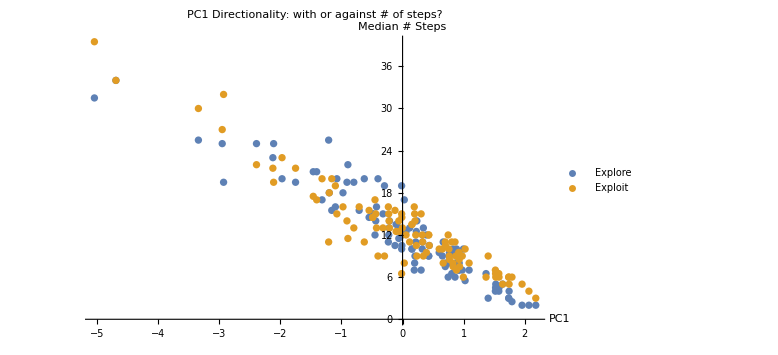

```mathematica
ListPlot[{{pc1,medianStepsMatrix[[;;,1]]}ᵀ,{pc1,medianStepsMatrix[[;;,2]]}ᵀ},AxesLabel->{"PC1", "Median # Steps"},PlotLegends->{"Explore", "Exploit"},PlotLabel->"PC1 Directionality: with or against # of steps?", ImageSize->Large]
```

Now create the new variables after forcing the direction (PC1 decreases with phase durations, PC2 increases with the difference between exploit-explore):

```mathematica
switchingRate=(-(Sign@SpearmanRho[pc1,medianStepsMatrix[[;;,1]]])pc1)~Prepend~"switching_rate";
```

```mathematica
tendencyToExploit=((Sign@SpearmanRho[pc2,medianStepsMatrix[[;;,2]]-medianStepsMatrix[[;;,1]]])pc2)~Prepend~"tendency_to_exploit";
```

```mathematica
withLabels=(withLabelsᵀ~Append~switchingRate~Append~tendencyToExploit)ᵀ;
```

```mathematica
withLabels//Dimensions
```

{103,41}

export results:

```mathematica
Export["N:\\Experiments\\CFG_TTT\\standard_measures\\standard_measures.csv",withLabels];
```

## Export gallery timings and orig

Use clusterFinder to wrap your findclusters version of choice, such that the resulting function will only require one argument:

```mathematica
clusterFinder[parsedGameData_]:=findclustersMRI[parsedGameData,2,0.9,False]
```

Create the Orig mapper:

```mathematica
Orig=Dispatch[Thread[(#[[1]]/.R)->-Log10[N@((#[[2]])/(Total@#[[2]]))]]&@(Tally[Cases[filteredData,{x_List,y_Real,z_Real}:>x,∞]]ᵀ)];
```

Create the csv:

```mathematica
galleryShapesIdx=Position[filteredData[[;;,3]],{_List,_,_}];exploreShapesIdx=Flatten[#,1]&@Table[{i,#}&/@segmentShapes[filteredData[[i]],clusterFinder][[1]],{i,1,Length@filteredData}];exploitShapesIdx=Flatten[#,1]&@Table[{i,#}&/@segmentShapes[filteredData[[i]],clusterFinder][[2]],{i,1,Length@filteredData}];exploreGalleryIdx=exploreShapesIdx∩galleryShapesIdx;exploitGalleryIdx=exploitShapesIdx∩galleryShapesIdx;exploreInfo={filteredData[[#[[1]],1]]}~Join~filteredData[[#[[1]],3,#[[2]]]]~Join~{"explore"}/.R&/@exploreGalleryIdx;exploitInfo={filteredData[[#[[1]],1]]}~Join~filteredData[[#[[1]],3,#[[2]]]]~Join~{"exploit"}/.R&/@exploitGalleryIdx;allInfo=exploreInfo~Join~exploitInfo;
origValues=allInfo[[;;,2]]/.orig;
allInfo=(allInfoᵀ~Append~origValues)ᵀ;
sortedInfo=SortBy[allInfo,{First,#[[3]]&}];
final=Prepend[sortedInfo,{"subj ID","shape ID","creation time","saving time","phase","originality"}];
final//TableForm
```

#### Export the csv:

```mathematica
Export[FileNameJoin@{homeDir,"gallery_timings_"<>DateString[{"Day","Month","Year"}]<>".csv"},final]
```

## Visualize data

### Game measures

```mathematica
TableForm[noLabels,TableDirections->Row,TableHeadings->{None,withLabels//First}]
```

ID | 122319 | 1396376 | 1458241 | 1628596 | 1692232 | 1716463 | 2133836 | 2168723 | 2185902 | 3064327 | 3284103 | 3317839 | 3363591 | 3374464 | 340445 | 3679849 | 3791727 | 4748029 | 477282 | 4831602 | 572571 | 5751980 | 6102006 | 6128847 | 6549967 | 6855705 | 7225713 | 7289058 | 7510218 | 7594903 | 8021243 | 8184961 | 8286321 | 8326152 | 8481610 | 860410 | 8614913 | 9203764 | 9225617 | 9355450 | 9442182 | 9532934 | 9600597 | 9608752 | 9766445
Date/Time | Sun 9 May 2021 10:07:13GMT+3. | Tue 13 Apr 2021 12:32:54GMT+3. | Mon 12 Apr 2021 11:06:07GMT+3. | Sun 25 Apr 2021 13:43:18GMT+3. | Sun 9 May 2021 10:06:56GMT+3. | Thu 8 Apr 2021 12:49:31GMT+3. | Sun 9 May 2021 10:06:10GMT+3. | Mon 3 May 2021 12:39:04GMT+3. | Tue 13 Apr 2021 11:40:20GMT+3. | Tue 13 Apr 2021 11:42:08GMT+3. | Thu 8 Apr 2021 11:36:44GMT+3. | Sun 25 Apr 2021 10:31:36GMT+3. | Mon 3 May 2021 12:36:54GMT+3. | Thu 8 Apr 2021 12:48:12GMT+3. | Thu 8 Apr 2021 12:50:40GMT+3. | Thu 8 Apr 2021 12:50:42GMT+3. | Mon 12 Apr 2021 11:11:33GMT+3. | Thu 8 Apr 2021 11:36:57GMT+3. | Sun 14 Mar 2021 10:11:49GMT+3. | Sun 25 Apr 2021 11:34:29GMT+3. | Tue 13 Apr 2021 11:50:04GMT+3. | Thu 8 Apr 2021 12:51:22GMT+3. | Mon 3 May 2021 12:50:14GMT+3. | Sun 9 May 2021 10:23:31GMT+3. | Thu 8 Apr 2021 12:52:44GMT+3. | Tue 13 Apr 2021 11:57:15GMT+3. | Sun 9 May 2021 12:14:12GMT+3. | Sun 9 May 2021 10:23:45GMT+3. | Mon 3 May 2021 12:36:41GMT+3. | Thu 22 Apr 2021 13:21:18GMT+3. | Mon 3 May 2021 12:53:17GMT+3. | Sun 9 May 2021 11:07:27GMT+3. | Tue 13 Apr 2021 12:49:35GMT+3. | Sun 2 May 2021 12:05:19GMT+3. | Sun 2 May 2021 10:09:08GMT+3. | Sun 9 May 2021 12:19:03GMT+3. | Sun 25 Apr 2021 13:37:13GMT+3. | Thu 8 Apr 2021 11:54:48GMT+3. | Mon 3 May 2021 13:38:53GMT+3. | Thu 8 Apr 2021 11:52:55GMT+3. | Sun 9 May 2021 10:24:56GMT+3. | Sun 25 Apr 2021 13:41:39GMT+3. | Thu 8 Apr 2021 11:46:43GMT+3. | Mon 3 May 2021 12:47:26GMT+3. | Sun 9 May 2021 12:25:56GMT+3.
Total 
Play 
Time | 719.873 | 710.633 | 719.762 | 719.06 | 719.087 | 719.858 | 719.898 | 719.878 | 708.406 | 719.109 | 720.276 | 719.406 | 719.813 | 719.728 | 718.689 | 720.26 | 699.381 | 719.15 | 718.493 | 716.338 | 720.4 | 720.956 | 716.312 | 718.632 | 719.264 | 719.187 | 720.144 | 719.157 | 720.466 | 719.459 | 711.491 | 714.583 | 721.082 | 720.828 | 718.839 | 720.846 | 718.132 | 721.072 | 703.225 | 703.429 | 718.866 | 719.538 | 706.321 | 711.786 | 720.669
Total 
# 
moves | 313 | 205 | 209 | 186 | 200 | 229 | 331 | 278 | 239 | 211 | 298 | 267 | 219 | 209 | 260 | 325 | 186 | 213 | 238 | 155 | 240 | 227 | 167 | 312 | 227 | 175 | 276 | 219 | 207 | 174 | 206 | 218 | 185 | 221 | 205 | 246 | 312 | 290 | 223 | 215 | 160 | 312 | 231 | 209 | 259
Average 
Speed | 0.434799 | 0.288475 | 0.290374 | 0.258671 | 0.27813 | 0.318118 | 0.459787 | 0.386177 | 0.337377 | 0.293419 | 0.41373 | 0.37114 | 0.304246 | 0.290387 | 0.36177 | 0.451226 | 0.265949 | 0.296183 | 0.331249 | 0.216378 | 0.333148 | 0.31486 | 0.233139 | 0.434158 | 0.3156 | 0.24333 | 0.383257 | 0.304523 | 0.287314 | 0.241848 | 0.289533 | 0.305073 | 0.256559 | 0.306592 | 0.285182 | 0.341266 | 0.434461 | 0.402179 | 0.31711 | 0.305646 | 0.222573 | 0.433612 | 0.327047 | 0.293628 | 0.359388
galleries
# | 72 | 47 | 54 | 22 | 34 | 19 | 36 | 50 | 23 | 48 | 31 | 34 | 40 | 35 | 35 | 14 | 30 | 32 | 32 | 19 | 19 | 33 | 17 | 60 | 27 | 30 | 179 | 39 | 33 | 62 | 46 | 18 | 60 | 12 | 109 | 56 | 57 | 39 | 94 | 68 | 30 | 112 | 23 | 78 | 23
self 
avoidance | 0.824916 | 0.930851 | 0.958115 | 0.966667 | 0.87027 | 0.955157 | 0.861736 | 0.880309 | 0.834862 | 0.966184 | 0.881944 | 0.948413 | 0.976415 | 0.91 | 0.919355 | 0.92926 | 0.977654 | 0.945 | 0.901869 | 0.860927 | 0.905579 | 0.975845 | 0.943396 | 0.955631 | 0.886364 | 0.945122 | 0.953125 | 0.928571 | 0.935644 | 0.929412 | 0.939698 | 0.962085 | 0.95082 | 0.980198 | 0.965 | 0.875519 | 0.868056 | 0.844203 | 0.95283 | 0.84466 | 0.898649 | 0.90681 | 0.876777 | 0.946602 | 0.921162
clusters
# | 15. | 8. | 12. | 3. | 6. | 4. | 7. | 9. | 4. | 8. | 5. | 6. | 7. | 6. | 6. | 3. | 6. | 8. | 4. | 3. | 3. | 5. | 2. | 12. | 4. | 4. | 31. | 5. | 6. | 8. | 7. | 3. | 10. | 2. | 18. | 9. | 12. | 6. | 17. | 11. | 4. | 15. | 3. | 15. | 4.
% shapes 
in exp | 0.166667 | 0.106383 | 0.037037 | 0.454545 | 0.264706 | 0.210526 | 0.222222 | 0.16 | 0.173913 | 0.270833 | 0.387097 | 0.235294 | 0.125 | 0.228571 | 0.142857 | 0.0714286 | 0.266667 | 0.15625 | 0.21875 | 0.157895 | 0.157895 | 0.363636 | 0.352941 | 0.2 | 0.185185 | 0.3 | 0.212291 | 0.333333 | 0.181818 | 0.322581 | 0.282609 | 0.277778 | 0.166667 | 0.166667 | 0.137615 | 0.160714 | 0.140351 | 0.230769 | 0.180851 | 0.176471 | 0.2 | 0.1875 | 0.391304 | 0.128205 | 0.347826
% time 
in exp | 0.167285 | 0.136746 | 0.0272685 | 0.473279 | 0.207612 | 0.141289 | 0.248803 | 0.151375 | 0.208336 | 0.254398 | 0.427409 | 0.241968 | 0.0901735 | 0.199848 | 0.153674 | 0. | 0.266253 | 0.117732 | 0.154463 | 0.13721 | 0.132697 | 0.320094 | 0.375265 | 0.209979 | 0.0759287 | 0.287787 | 0.220121 | 0.38246 | 0.162 | 0.352668 | 0.292727 | 0.177044 | 0.183473 | 0.0756485 | 0.108434 | 0.119583 | 0.108868 | 0.209248 | 0.171436 | 0.212169 | 0.220849 | 0.18356 | 0.251235 | 0.104232 | 0.326894
exp 
optimality | 0.732143 | 0.5 | 0.690476 | 0.4 | 0.571429 | 0.458333 | 0.347222 | 0.5 | 0.444444 | 0.7 | 0.598214 | 0.30625 | 0.708333 | 0.633333 | 0.375 | 0.0816327 | 0.5625 | 0.5 | 0.428571 | 0.461538 | 0.6 | 0.535714 | 0.331579 | 0.5 | 0.5625 | 0.571429 | 0.55 | 0.5 | 0.472222 | 1. | 0.8 | 0.5 | 1. | 0.583333 | 1. | 0.75 | 0.5 | 0.714286 | 1. | 0.547619 | 0.75 | 0.583333 | 0.625 | 1. | 0.75
scav 
optimality | 0.8 | 0.666667 | 0.8 | 0.4375 | 0.75 | 0.375 | 0.577778 | 0.666667 | 0.5 | 0.791667 | 0.428571 | 0.5 | 0.733333 | 0.625 | 0.5 | 0.263158 | 0.666667 | 0.5 | 0.5 | 0.4 | 0.5 | 0.571429 | 0.285714 | 0.666667 | 0.333333 | 0.666667 | 0.666667 | 0.666667 | 0.666667 | 1. | 0.75 | 0.3 | 0.857143 | 0.215278 | 1. | 0.75 | 0.5 | 0.666667 | 1. | 0.666667 | 0.5 | 0.5 | 0.273214 | 1. | 0.5
optimality
ratio | 0.915179 | 0.75 | 0.863095 | 0.914286 | 0.761905 | 1.22222 | 0.600962 | 0.75 | 0.888889 | 0.884211 | 1.39583 | 0.6125 | 0.965909 | 1.01333 | 0.75 | 0.310204 | 0.84375 | 1. | 0.857143 | 1.15385 | 1.2 | 0.9375 | 1.16053 | 0.75 | 1.6875 | 0.857143 | 0.825 | 0.75 | 0.708333 | 1. | 1.06667 | 1.66667 | 1.16667 | 2.70968 | 1. | 1. | 1. | 1.07143 | 1. | 0.821429 | 1.5 | 1.16667 | 2.28758 | 1. | 1.5
median # steps 
between shapes 
in exp | 10. | 10. | 7. | 21. | 13.5 | 23. | 16. | 12. | 25. | 10. | 19. | 15.5 | 11. | 10.5 | 20. | 34. | 7. | 14. | 14.5 | 15. | 25. | 13. | 19.5 | 13. | 17. | 14. | 2. | 9. | 12.5 | 4. | 8. | 25.5 | 7. | 37.5 | 2. | 6. | 9.5 | 20. | 4. | 9.5 | 8. | 2.5 | 35. | 4.5 | 15.
median # steps 
between shapes 
in scav | 6. | 13.5 | 9.5 | 17. | 12.5 | 21.5 | 13. | 13. | 19.5 | 7. | 9. | 16. | 16. | 15.5 | 11. | 34. | 9.5 | 9. | 15.5 | 13. | 27. | 9. | 32. | 11. | 20. | 13. | 3. | 12. | 12. | 6.5 | 9. | 30. | 9. | 65. | 5. | 12. | 8.5 | 15. | 7. | 10. | 10.5 | 6. | 22. | 6. | 14.5
exp
speed | 0.474688 | 0.310249 | 0.313764 | 0.258867 | 0.276317 | 0.326679 | 0.479694 | 0.40386 | 0.368026 | 0.277731 | 0.399938 | 0.355191 | 0.313518 | 0.273375 | 0.382314 | 0.45356 | 0.241728 | 0.310495 | 0.293702 | 0.183518 | 0.376737 | 0.346125 | 0.229015 | 0.449199 | 0.26135 | 0.210499 | 0.394607 | 0.322692 | 0.288713 | 0.237145 | 0.279719 | 0.323533 | 0.258627 | 0.266675 | 0.243414 | 0.353985 | 0.427817 | 0.432194 | 0.311135 | 0.354117 | 0.222633 | 0.459102 | 0.36331 | 0.264385 | 0.364957
scav
speed | 0.427134 | 0.295223 | 0.27088 | 0.251108 | 0.318433 | 0.330341 | 0.451471 | 0.382312 | 0.334255 | 0.301636 | 0.359957 | 0.419543 | 0.302302 | 0.287542 | 0.325366 | 0.446749 | 0.356247 | 0.255577 | 0.289597 | 0.219191 | 0.337989 | 0.295434 | 0.201376 | 0.399921 | 0.314798 | 0.290418 | 0.457865 | 0.282949 | 0.279036 | 0.254167 | 0.293301 | 0.294828 | 0.252053 | 0.311028 | 0.319419 | 0.324365 | 0.422283 | 0.36995 | 0.332144 | 0.376498 | 0.226301 | 0.512924 | 0.312073 | 0.322197 | 0.408392
Orig | 2.83225 | 2.90259 | 3.09151 | 3.17351 | 2.81129 | 2.98962 | 2.77449 | 2.78186 | 2.9285 | 3.03787 | 2.85863 | 3.01215 | 2.98648 | 2.75181 | 2.79013 | 2.96895 | 2.90525 | 2.92232 | 2.8547 | 2.75797 | 2.59043 | 2.9141 | 2.8855 | 3.24768 | 2.84951 | 3.15742 | 3.07535 | 2.86019 | 2.84092 | 3.01887 | 2.85286 | 2.91281 | 2.99975 | 2.85152 | 3.03651 | 2.86337 | 2.90493 | 2.59445 | 3.13145 | 2.90502 | 2.844 | 3.02996 | 2.87856 | 2.97493 | 2.90421
Orig (united) | 3.16181 | 3.1984 | 3.74269 | 4.00248 | 3.10258 | 3.45331 | 3.00622 | 3.07905 | 3.17834 | 3.46923 | 3.2345 | 3.70386 | 3.47287 | 2.93875 | 2.9958 | 2.98693 | 3.14301 | 3.39133 | 3.16976 | 2.85892 | 2.75256 | 3.37411 | 3.46607 | 4.21281 | 3.26218 | 4.00618 | 3.61435 | 3.11158 | 3.10051 | 3.58482 | 3.12189 | 3.38505 | 3.44769 | 3.32555 | 3.56207 | 3.27002 | 3.35024 | 2.6408 | 3.80656 | 3.36052 | 3.31009 | 3.53178 | 3.30621 | 3.48261 | 3.22466
Orig 
exp | 2.89941 | 2.87652 | 3.01465 | 3.06668 | 2.72553 | 2.87036 | 2.771 | 2.76031 | 2.94392 | 3.05575 | 2.84103 | 2.9531 | 3.15487 | 2.96118 | 2.93447 | 2.91863 | 3.00475 | 2.74156 | 2.93624 | 2.5853 | 2.43254 | 2.9682 | 2.8291 | 3.30771 | 3.11317 | 3.25298 | 3.09099 | 3.07041 | 2.99577 | 3.08643 | 2.80673 | 2.84921 | 3.07283 | 3.23245 | 2.96732 | 2.83636 | 2.79368 | 2.57407 | 3.13636 | 2.78299 | 2.99457 | 3.11566 | 2.92989 | 3.11218 | 2.80341
Orig exp (united) | 3.2898 | 3.26462 | 3.68411 | 3.76122 | 3.01524 | 3.15118 | 3.10041 | 2.95053 | 3.28122 | 3.57952 | 3.2619 | 3.69046 | 3.77204 | 3.19323 | 3.21476 | 3.02531 | 3.18833 | 3.13904 | 3.37541 | 2.76976 | 2.50926 | 3.41647 | 3.21933 | 4.31448 | 3.67596 | 4.22357 | 3.59187 | 3.49129 | 3.31797 | 3.67086 | 3.02199 | 3.31352 | 3.63196 | 3.93505 | 3.54973 | 3.22656 | 3.19089 | 2.6507 | 3.86468 | 3.15524 | 3.5855 | 3.60728 | 3.19657 | 3.64686 | 3.13503
Orig 
scav | 2.79652 | 2.91256 | 3.11841 | 3.28034 | 2.87133 | 3.05919 | 2.77671 | 2.7911 | 2.92176 | 3.02807 | 2.87135 | 3.04435 | 2.92261 | 2.64258 | 2.7324 | 2.98907 | 2.83891 | 3.03078 | 2.81764 | 2.83766 | 2.64682 | 2.87893 | 2.92497 | 3.21292 | 2.7385 | 3.1021 | 3.06765 | 2.74247 | 2.7635 | 2.98426 | 2.87747 | 2.95328 | 2.96843 | 2.66105 | 3.06159 | 2.87325 | 2.95628 | 2.60586 | 3.12916 | 2.95954 | 2.78925 | 3.00002 | 2.83908 | 2.91392 | 2.98175
Orig scav (united) | 3.09373 | 3.17307 | 3.76319 | 4.24374 | 3.16371 | 3.62956 | 2.94627 | 3.13413 | 3.13333 | 3.40875 | 3.21471 | 3.71117 | 3.35939 | 2.80598 | 2.90821 | 2.97158 | 3.11279 | 3.54271 | 3.07629 | 2.90006 | 2.83945 | 3.34658 | 3.63878 | 4.15395 | 3.08796 | 3.88032 | 3.6254 | 2.89894 | 2.99177 | 3.54074 | 3.17516 | 3.43057 | 3.36872 | 3.0208 | 3.56655 | 3.28592 | 3.42379 | 2.63526 | 3.77931 | 3.45224 | 3.20994 | 3.5054 | 3.39054 | 3.40961 | 3.2936
Orig 
trans | 2.91377 | 2.92281 | 2.96581 | 3.1873 | 2.68523 | 2.85105 | 2.88101 | 2.73891 | 3.06689 | 3.13444 | 2.83119 | 2.93843 | 3.21044 | 2.95054 | 2.81752 | 2.78894 | 2.97255 | 2.93722 | 2.99645 | 2.81534 | 2.36426 | 2.92842 | 2.90634 | 3.30771 | 2.99645 | 3.30771 | 3.18505 | 3.17703 | 2.95384 | 3.01798 | 2.88469 | 3.13297 | 3.04218 | 3.30771 | 2.99914 | 2.8733 | 2.66832 | 2.66335 | 3.13703 | 2.88613 | 2.94036 | 3.06824 | 3.15208 | 3.16995 | 2.73423
Orig trans (united) | 3.32338 | 3.34188 | 3.57599 | 3.90763 | 2.81304 | 3.14721 | 3.27648 | 2.9554 | 3.4296 | 3.71706 | 3.2035 | 3.66497 | 3.77472 | 3.20708 | 2.99663 | 3.1085 | 3.1677 | 3.46798 | 3.42477 | 2.80983 | 2.37753 | 3.38502 | 3.62571 | 4.32551 | 3.53639 | 4.23714 | 3.71586 | 3.60241 | 3.41287 | 3.51875 | 3.20666 | 3.78506 | 3.61545 | 3.94374 | 3.59185 | 3.26028 | 2.91456 | 2.67256 | 3.85 | 3.30982 | 3.58013 | 3.5242 | 3.64206 | 3.6856 | 3.0615
Unique 
Shapes | 0.333333 | 0.319149 | 0.660377 | 0.809524 | 0.375 | 0.526316 | 0.114286 | 0.24 | 0.318182 | 0.510638 | 0.466667 | 0.636364 | 0.45 | 0.285714 | 0.323529 | 0.428571 | 0.5 | 0.516129 | 0.321429 | 0.210526 | 0.157895 | 0.515152 | 0.352941 | 0.9 | 0.423077 | 0.827586 | 0.656977 | 0.421053 | 0.34375 | 0.57377 | 0.333333 | 0.5 | 0.465517 | 0.333333 | 0.59434 | 0.4 | 0.462963 | 0.0540541 | 0.670213 | 0.403226 | 0.464286 | 0.574074 | 0.45 | 0.552632 | 0.478261
Unique 
Shapes exp | 0.0754717 | 0.0847458 | 0.213115 | 0.166667 | 0.078125 | 0.0857143 | 0.0298507 | 0.0606061 | 0.0909091 | 0.0933333 | 0.129032 | 0.0892857 | 0.0612245 | 0.109091 | 0.0816327 | 0.0454545 | 0.0727273 | 0.107143 | 0.0888889 | 0.0666667 | 0.0384615 | 0.118644 | 0.030303 | 0.210526 | 0.128205 | 0.2 | 0.135021 | 0.0952381 | 0.0588235 | 0.166667 | 0.0555556 | 0.0588235 | 0.153846 | 0.05 | 0.163934 | 0.0597015 | 0.1125 | 0. | 0.16129 | 0.0568182 | 0.108108 | 0.163934 | 0.0833333 | 0.127451 | 0.133333
Unique 
Shapes scav | 0.266667 | 0.352941 | 0.725 | 1. | 0.4 | 0.666667 | 0.136364 | 0.285714 | 0.375 | 0.483871 | 0.444444 | 0.619048 | 0.37931 | 0.173913 | 0.25 | 0.4 | 0.444444 | 0.65 | 0.35 | 0.307692 | 0.214286 | 0.45 | 0.3 | 0.842105 | 0.388889 | 0.736842 | 0.632479 | 0.291667 | 0.227273 | 0.525 | 0.333333 | 0.545455 | 0.390244 | 0.125 | 0.615385 | 0.425 | 0.5 | 0.0833333 | 0.703125 | 0.444444 | 0.4 | 0.5375 | 0.5 | 0.490566 | 0.538462
# clusters 
in GC | 3. | 2. | 0. | 0. | 1. | 0. | 1. | 2. | 0. | 0. | 1. | 0. | 1. | 0. | 2. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 1. | 2. | 0. | 2. | 2. | 0. | 0. | 0. | 2. | 1. | 0. | 3. | 1. | 1. | 3. | 1. | 0. | 2. | 1.
% clusters 
in GC | 0.12 | 0.153846 | 0. | 0. | 0.0714286 | 0. | 0.0714286 | 0.133333 | 0. | 0. | 0.0769231 | 0. | 0.0909091 | 0. | 0.2 | 0. | 0. | 0.0833333 | 0.1 | 0.166667 | 0.2 | 0.0769231 | 0. | 0. | 0.125 | 0. | 0.0169492 | 0.142857 | 0. | 0.0952381 | 0.125 | 0. | 0. | 0. | 0.0689655 | 0.0666667 | 0. | 0.214286 | 0.0333333 | 0.047619 | 0.375 | 0.0344828 | 0. | 0.0833333 | 0.1
max Δt 
(min) | 0.360067 | 0.457967 | 0.257083 | 0.855683 | 0.3147 | 1.33033 | 0.292867 | 0.3516 | 0.2939 | 0.281033 | 0.191283 | 1.2279 | 0.3076 | 0.3346 | 0.540817 | 0.132333 | 0.7447 | 0.294167 | 0.397467 | 0.444617 | 0.290517 | 0.183517 | 0.410567 | 0.164083 | 0.198033 | 1.05493 | 0.576017 | 0.24585 | 0.358 | 0.357367 | 0.3189 | 0.675467 | 0.4298 | 0.364067 | 0.401333 | 0.226967 | 0.286517 | 0.324333 | 0.322217 | 0.496467 | 0.751917 | 0.138717 | 0.477283 | 0.246167 | 0.607817

### Clusters shapes and timing

Each element in “Column” below is plotted below the previous one. Here there are 4 elements: 
(1) a graph of clusters with delta-t (time difference between gallery shapes) on the Y axis
(2) a graph of clusters with optimality on the Y axis, based on a specific threshold
(3) a graph of clusters with optimality on the Y axis, based on a different threshold
(4) The actual shapes of each cluster (clusters separated by a comma)

```mathematica
clustered2=findclusters2/@filteredData;
clusteredMRI09=findclustersMRI[#,2,0.9]&/@filteredData;
clusteredMRI09Seqs=findclustersMRI[#,2,0.9]&/@reduceSeqs/@filteredData;
Manipulate[
Column[
{"Subject ID: "<>ToString@filteredData[[i,1]],
ListLinePlot[Map[Tooltip[#[[{2,1}]],ShapePlot5a[#[[-1]]/.backr]]&,clustered2[[i]][[;;,;;,{1,2,-1}]],{2}],AspectRatio->.1,AxesLabel->{"t","Δt"},PlotMarkers->{Automatic, 10},PlotRange->{All,maxtime},ImageSize->1000],
ListLinePlot[Map[Tooltip[{#[[2]],(#[[3]])/(#[[4]])},ShapePlot5a[#[[-1]]/.backr]]&,clusteredMRI09[[i]],{2}],AxesLabel->{"t","optimality"},PlotLabel->"0.9",AspectRatio->.1,PlotMarkers->{Automatic, 10},PlotRange->{All,maxtime},ImageSize->1000],
ListLinePlot[Map[Tooltip[{#[[2]],(#[[3]])/(#[[4]])},ShapePlot5a[#[[-1]]/.backr]]&,clusteredMRI09Seqs[[i]],{2}],AxesLabel->{"t","optimality"},PlotLabel->"0.9+seq",AspectRatio->.1,PlotMarkers->{Automatic, 10},PlotRange->{All,maxtime},ImageSize->1000],
Row/@Map[ShapePlot5a[#/.backr]&,clustered2[[i]][[;;,;;,-1]],{2}]}],
{i,1,Length@filteredData,1},{{maxtime,All},4,20}]
```

### All shapes per game

```mathematica
Manipulate[Column[{"Subject ID: "<>ToString@filteredData[[i,1]], ShapePlot5a[#[[1]],BackgroundColor->If[Length@#==3,Red,Black]]&/@filteredData[[i,-2]]}],{i,1,Length@filteredData,1}]
```